```mathematica
m=.0358*10^6/(2.998*10^8)^2;(* eV/c^2 *)
V1=.5;(* eV *)
V2=1.13;(* eV *)
L1=4*10^-9; (* m *)
L2 = 3*10^-9; (* m *)
G=3.6*10^-9; (* m *)
hb=6.582*10^-16 ;(* eV*s *)
kp2=Sqrt[2*m*(E0-V2)/hb^2];
kp1=Sqrt[2*m*(E0-V1)/hb^2];
kf=Sqrt[2*m*E0/hb^2];
```

```mathematica
P1=Inverse[{{1,1},{kf,-kf}}].{{1,1},{kp1,-kp1}};
```

```mathematica
P2=Inverse[{{Exp[I*kp1*L1],Exp[-I*kp1*L1]},{kp1*Exp[I*kp1*L1],-kp1*Exp[-I*kp1*L1]}}].{{Exp[I*kf*L1],Exp[-I*kf*L1]},{kf*Exp[I*kf*L1],-kf*Exp[-I*kf*L1]}};
```

```mathematica
P3=Inverse[{{Exp[I*kf*(G+L1)],Exp[-I*kf*(G+L1)]},{kf*Exp[I*kf*(G+L1)],-kf*Exp[-I*kf*(G+L1)]}}].{{Exp[I*kp2*(G+L1)],Exp[-I*kp2*(G+L1)]},{kp2*Exp[I*kp2*(L1+G)],-kp2*Exp[-I*kp2*(L1+G)]}};
```

```mathematica
P4=Inverse[{{Exp[I*kp2*(G+L1+L2)],Exp[-I*kp2*(G+L1+L2)]},{kp2*Exp[I*kp2*(G+L1+L2)],-kp2*Exp[-I*kp2*(G+L1+L2)]}}].{{Exp[I*kf*(G+L1+L2)],Exp[-I*kf*(G+L1+L2)]},{kf*Exp[I*kf*(G+L1+L2)],-kf*Exp[-I*kf*(G+L1+L2)]}};
```

```mathematica
TransMat=P1.P2.P3.P4;
```

```mathematica
TC=TransMat[[1]][[1]];
```

```mathematica
Tp=1/(Abs[TC]^2);
```

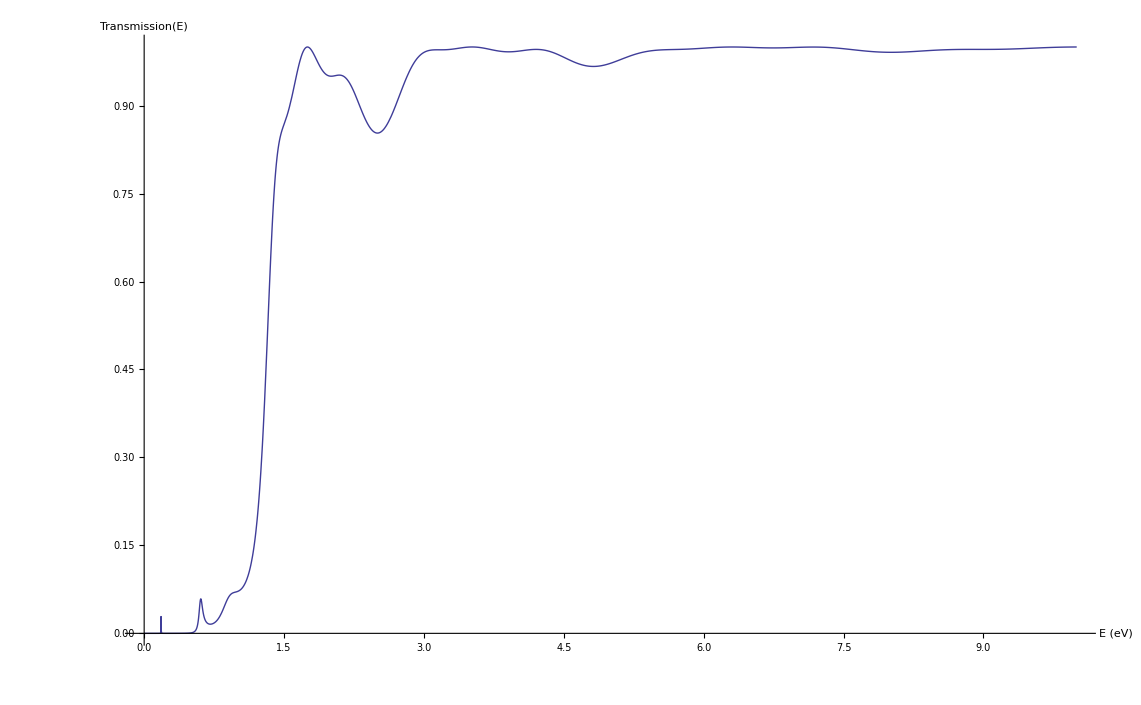

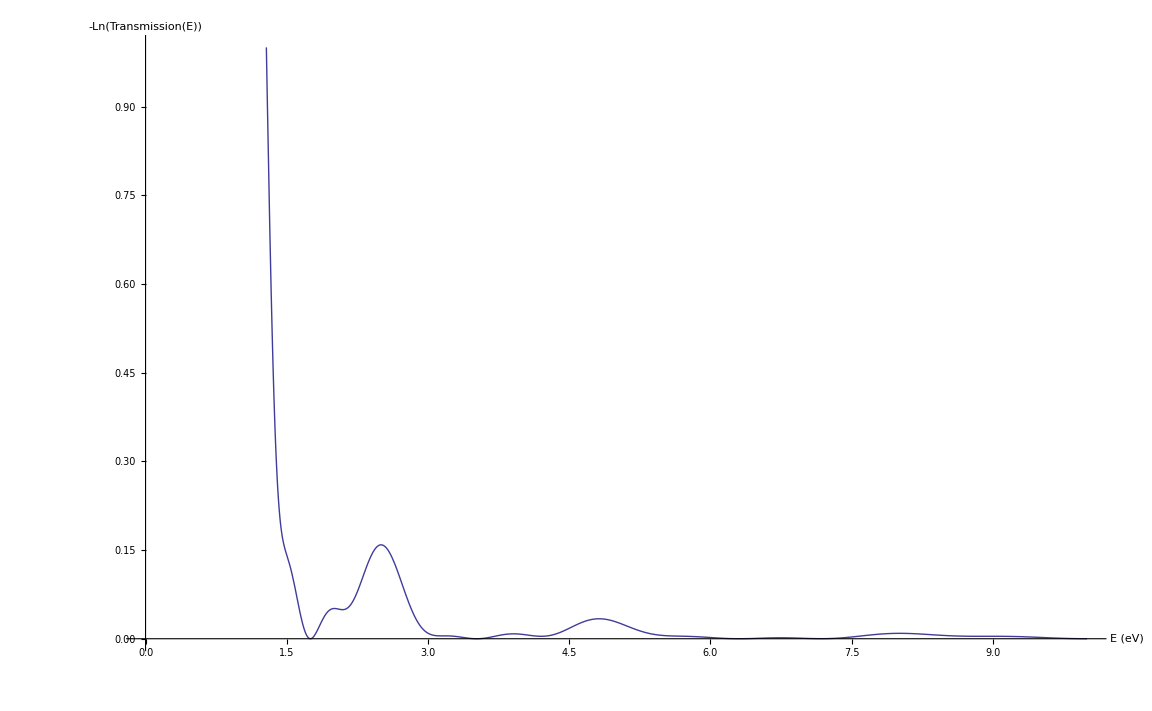

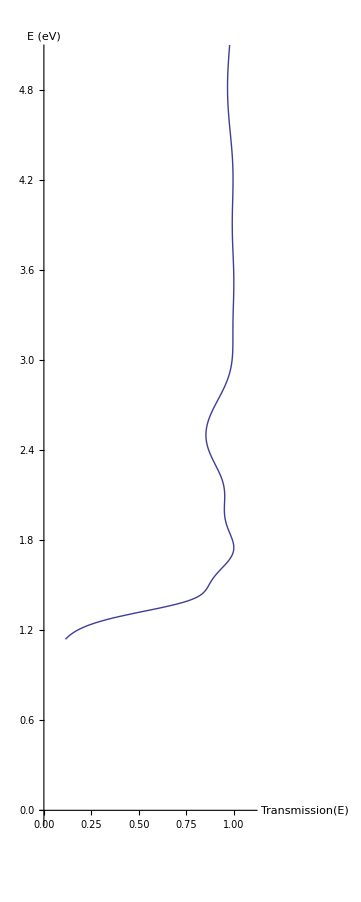

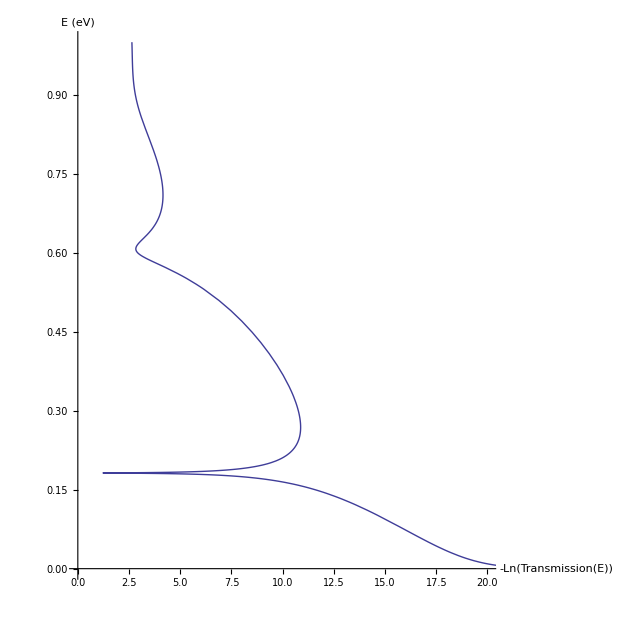

```mathematica
Quiet[Plot[Tp,{E0,0,10},PlotRange->{{0,10},{0,1}},AxesLabel->{"E (eV)","Transmission(E)"}]]
Quiet[Plot[-Log[Tp],{E0,0,10},PlotRange->{{0,10},{0,1}},AxesLabel->{"E (eV)","-Ln(Transmission(E))"}]]
Quiet[ParametricPlot[{Tp,E0},{E0,1.14,10},PlotRange-> {{0,1.1},{0,5}},AxesLabel->{"Transmission(E)","E (eV)"}]]
Quiet[ParametricPlot[{-Log[Tp],E0},{E0,0,1},PlotRange->{{0,20},{0,1}},AxesLabel->{"-Ln(Transmission(E))","E (eV)"},AspectRatio->1/1]]
```